## Kerr Raytracing

### Review of Kerr black holes and null geodesics

#### Kerr metric

The metric for a black hole with mass M and angular momentum J in Boyer-Lindquist coordinates (t,r,θ,ϕ) is

ds^2==-(1-(r_s r)/Σ)dt^2+Σ/Δ dr^2+Σ dθ^2+(r^2+a^2+(r_s r a^2)/Σ Sin^2[θ])Sin^2[θ]dϕ^2-(2 r_s r a Sin^2[θ])/Σ dt dϕ ,

where

r_s==2 G_N M,    a==J/M,    Σ==r^2+a^2 Cos^2[θ]    and    Δ==r^2-r_s r+a^2 .

The inner and outer surfaces of the ergosphere and inner and outer (event) horizons are located at

r_E^±==r_s/2±√((r_s/2)^2-a^2 Cos^2[θ]),    r_H^±==r_s/2±√((r_s/2)^2-a^2) .

From this we find the extremality bound, (|a|)/(G_N M)==(|J|)/(G_N M^2)≤1. It will be useful to work in units where G_N M==1, so that r_s==2 and a∈[-1,1].

```mathematica
Σ[r_,θ_,a_]:=r^2+a^2 Cos[θ]^2;
Δ[r_,a_]:=r^2-2r+a^2;
```

```mathematica
coord={tt,rr,θθ,ϕϕ};
metric=Simplify@({{-(1-(2rr)/Σ[rr,θθ,a]), 0, 0, -(2rr a Sin[θθ]^2)/Σ[rr,θθ,a]}, {0, Σ[rr,θθ,a]/Δ[rr,a], 0, 0}, {0, 0, Σ[rr,θθ,a], 0}, {-(2rr a Sin[θθ]^2)/Σ[rr,θθ,a], 0, 0, (rr^2+a^2+(2rr a^2)/Σ[rr,θθ,a] Sin[θθ]^2)Sin[θθ]^2}});
$Assumptions=And[rr>2,-1<a<1,0<θθ<π,0<ϕϕ<2π];
metricsign=-1;
<<Diffgeo`
```

```mathematica
zeroQ@Einstein
```

True

#### Conserved quantities and null geodesics

There are two ‘obvious’ conserved quantities associated to the Killing vectors ∂_t  and ∂_ϕ , which are the energy E==-p_t and angular momentum L_z==-p_ϕ. There is a third conserved quantity, the Carter constant Q==p_θ^2-Cos^2[θ](a^2 E^2-L_z^2 Csc^2[θ]), which is associated to a Killing tensor. These three constants, along with p_μ p^μ==0, are enough to determine a null geodesic uniquely.

With affine parameter λ (so that (ⅆ x^μ)/ⅆλ==p^μ), trajectories are found by solving the following,

Σ ⅆr/ⅆλ==±√R[r]
Σ ⅆθ/ⅆλ==±√Θ[θ]
Σ ⅆϕ/ⅆλ==-(a E-L_z Csc^2[θ])+a/Δ P[r]
Σ ⅆt/ⅆλ==-a(a E Sin^2[θ]-L_z)+(r^2+a^2)/Δ P[r]

where the ‘potentials’ are

P[r]==E(r^2+a^2)-a L_z
Θ[θ]==Q+Cos^2[θ](a^2 E^2-L_z^2 Csc^2[θ])
R[r]==P[r]^2-Δ(Q+(a E-L_z)^2)

```mathematica
dtdλ[r_,θ_,a_,e_,Lz_,Q_]:=(-a^2 e Sin[θ]^2+a Lz+(r^2+a^2)/Δ[r,a] P[r,a,e,Lz])/Σ[r,θ,a];
drdλ[r_,θ_,a_,e_,Lz_,Q_,signr_]:=signr (√R[r,a,e,Lz,Q])/Σ[r,θ,a];
dθdλ[r_,θ_,a_,e_,Lz_,Q_,signθ_]:=signθ (√Θ[θ,a,e,Lz,Q])/Σ[r,θ,a];
dϕdλ[r_,θ_,a_,e_,Lz_,Q_]:=(-a e+Lz Csc[θ]^2+a/Δ[r,a] P[r,a,e,Lz])/Σ[r,θ,a];
```

```mathematica
P[r_,a_,e_,Lz_]:=e(r^2+a^2)-a Lz;
Θ[θ_,a_,e_,Lz_,Q_]:=Q+Cos[θ]^2(a^2 e^2-Lz^2 Csc[θ]^2);
R[r_,a_,e_,Lz_,Q_]:=P[r,a,e,Lz]^2-Δ[r,a]((a e-Lz)^2+Q);
```

#### Change of coordinates

There is a coordinate singularity at the inner and outer horizons, which makes numerically solving for null geodesics near the outer horizon delicate. The coordinate singularity at the outer horizon may be removed by working with v and φ, rather than t and ϕ, defined by

ⅆv==ⅆt+(r^2+a^2)/Δ ⅆr
ⅆφ==ⅆϕ+a/Δ ⅆr

```mathematica
dvdλ[r_,θ_,a_,e_,Lz_,Q_,signr_]:=dtdλ[r,θ,a,e,Lz,Q]+(r^2+a^2)/Δ[r,a] drdλ[r,θ,a,e,Lz,Q,signr];
dφdλ[r_,θ_,a_,e_,Lz_,Q_,signr_]:=dϕdλ[r,θ,a,e,Lz,Q]+a/Δ[r,a] drdλ[r,θ,a,e,Lz,Q,signr];
```

One can integrate to find the coordinates v and φ:

v==t+T[r], where T'[r]==(r^2+a^2)/Δ
φ==ϕ+Φ[r], where Φ'[r]==a/Δ

```mathematica
T[r_,a_]:=r+1/2 Log[Δ[r,a]^2/16]+1/(2 √(1-a^2))Log[((r-1-√(1-a^2))/(r-1+√(1-a^2)))^2];
Φ[r_,a_]:=a/(4 √(1-a^2))Log[((r-1-√(1-a^2))/(r-1+√(1-a^2)))^2];
And[D[T[r,a], r]==(r^2+a^2)/Δ[r,a],D[Φ[r,a], r]==a/Δ[r,a]]//Simplify
```

True

### Null geodesics and images

The ‘camera’ points radially with an array of ‘pixels’ a distance Δr from the focus with size Δx × Δy (think pinhole camera). For each pixel the constants e,L_z,Q are found for that geodesic. The geodesic equations are integrated until some stopping condition is met.

#### E,L_z,Q for given initial conditions

```mathematica
Spherical[x_,y_,z_,α_,β_,γ_]:=ToSphericalCoordinates[RotationMatrix[γ,{0,0,1}].RotationMatrix[β,{1,0,0}].RotationMatrix[α,{0,0,1}].{x,y,z}];
```

```mathematica
GetxyeLzQarray[a_,rcam_,Δr_,Δx_,Δy_,xres_,yres_,α_,β_,γ_]:=Module[{focus,pixels,x,y,i,j,xyeLzQ},
focus=Spherical[0,0,rcam,α,β,γ];
pixels=Table[{x,y,focus-Spherical[x,y,rcam+Δr,α,β,γ]},{y,-Δy,Δy,(2Δy)/(yres-1)},{x,-Δx,Δx,(2Δx)/(xres-1)}];
xyeLzQ=Table[{
pixels[[i,j,1]],
pixels[[i,j,2]],
{Sign[pixels[[i,j,3,1]]],Sign[pixels[[i,j,3,2]]]},
{e,Lz,Q}/.First@NSolve[{pixels[[i,j,3]]=={
drdλ[rcam,β,a,e,Lz,Q,Sign[pixels[[i,j,3,1]]]],
dθdλ[rcam,β,a,e,Lz,Q,Sign[pixels[[i,j,3,2]]]],
dϕdλ[rcam,β,a,e,Lz,Q]
},e>0},{e,Lz,Q}]
},{i,yres},{j,xres}];
Return[xyeLzQ];
];
```

#### Integration

```mathematica
GetNullGeodesic[t0_,r0_,θ0_,ϕ0_,a_,eLzQ_,signs_,λmax_,rin_,rout_]:=
Module[{v0=t0+T[r0,a],φ0=ϕ0+Φ[r0,a],e=eLzQ[[1]],Lz=eLzQ[[2]],Q=eLzQ[[3]],eqns,init,stopCond,soln,domain},
eqns=Simplify@{
v'[λ]==Re@dvdλ[r[λ],θ[λ],a,e,Lz,Q,signr[λ]],
r'[λ]==Re@drdλ[r[λ],θ[λ],a,e,Lz,Q,signr[λ]],
θ'[λ]==Re@dθdλ[r[λ],θ[λ],a,e,Lz,Q,signθ[λ]],
φ'[λ]==Re@dφdλ[r[λ],θ[λ],a,e,Lz,Q,signr[λ]]
};
init={v[0]==v0,r[0]==r0,θ[0]==θ0,φ[0]==φ0,signr[0]==signs[[1]],signθ[0]==signs[[2]]};

stopCond="None";
soln=First@NDSolve[{eqns,init,
WhenEvent[r[λ]≤1,{stopCond="Horz","StopIntegration"}],
WhenEvent[r[λ]≥1.5r0,{stopCond="Esc","StopIntegration"}],
WhenEvent[θ[λ]>π/2&&rin≤r[λ]≤rout,{stopCond="Above","StopIntegration"}],
WhenEvent[θ[λ]<π/2&&rin≤r[λ]≤rout,{stopCond="Below","StopIntegration"}],
WhenEvent[θ[λ]<0.001,{signθ[λ]->-signθ[λ],φ[λ]->φ[λ]+π}],
WhenEvent[θ[λ]>π-0.001,{signθ[λ]->-signθ[λ],φ[λ]->φ[λ]+π}],
WhenEvent[R[r[λ],a,e,Lz,Q]<0.001,{r[λ]->r[λ]-signr[λ]0.001,signr[λ]->-signr[λ]}],
WhenEvent[Θ[θ[λ],a,e,Lz,Q]<0.0001,{θ[λ]->θ[λ]-signθ[λ]0.0001,signθ[λ]->-signθ[λ]}]
},
{v,r,θ,φ,signr,signθ},{λ,0,λmax},DiscreteVariables->{signr,signθ}];
Return[{soln, stopCond}];
];
```

```mathematica
GetNullTraj[soln_,adj_]:=Module[{λm,x,y,z},
λm=(r/.soln)["Domain"][[1,2]];
x=r[λ λm]Sin[θ[λ λm]]Cos[φ[λ λm]-adj Φ[r[λ λm]]];
y=r[λ λm]Sin[θ[λ λm]]Sin[φ[λ λm]-adj Φ[r[λ λm]]];
z=r[λ λm]Cos[θ[λ λm]];
Return[{x,y,z}/.soln];
];
```

#### Redshift

Would like to understand the redshift (blueshift) between the source and detector (camera). The energy of a photon is measured by

ω=-u^μ p_μ

for observer 4-velocity u^μ. Let’s suppose that the source is in some (stable) equitorial, circular orbit and that the detector is at some fixed r,θ,ϕ so that ω_detector==-u^t p_t. One can show that the time-like geodesic equations in the equitorial plane for fixed r determines u^μ entirely (recall that a^2≤M^2):

u^t==-(r^(3/2)±a √M)/(√(r^2(r-3M)±2a √M r^(3/2))), u^ϕ==∓(√M)/(√(r^2(r-3M)±2a √M r^(3/2)))

The two signs are for co- and counter-rotating. Notice that

dϕ/dt==u^ϕ/u^t==±(√M)/(r^(3/2)±a √M)

which reduces to Kepler’s 3^d law for a==0. From the form of u^t,u^ϕ we can identify the minimal r for which a circular orbit exists:

r(r-3M)^2-4M a^2==0

This is at least M at most 4M, changing as a ranges in -M≤a≤M.

Recall that p^μ==dx^μ/dλ for the null geodesic, with λ free to be rescaled. We can compute ω_detect/ω_source unambiguously, however.

ω_source==[-g_tt u_source^t p^t-g_tϕ(u_source^t p^ϕ+u_source^ϕ p^t)-g_ϕϕ u_source^ϕ p^ϕ]_(x^μ==source)
ω_detect==[-g_tt u_detect^t p^t]_(x^μ==detect)

```mathematica
RedShiftNaive[geo_]:=Module[{λm,r0,θ0},
λm=(r/.geo)["Domain"][[1,2]];
r0=r[0]/.geo;
θ0=θ[0]/.geo;
Return[√((-metric[[tt,tt]]/.{rr->r[λm],θθ->θ[λm]}/.geo)/(-metric[[tt,tt]]/.{rr->r0,θθ->θ0}))];
];
```

```mathematica
RedShift[geo_]:=Module[{λm,ωs,ωd},
λm=(r/.geo)["Domain"][[1,2]];
ωs=((√r[λm](r[λm]-2)+a)(v'[λm]-(r[λm]^2+a^2)/Δ[r[λm],a] r'[λm])-(r[λm]^2-2a √r[λm]+a^2)(φ'[λm]-a/Δ[r[λm],a] r'[λm]))/(√(r[λm]^2(r[λm]-3)+2a r[λm]^(3/2)))/.geo;
ωd=((r[0]-2)(r[0]^(3/2)+a)(v'[0]-(r[0]^2+a^2)/Δ[r[0],a] r'[0]))/(r[0] √(r[0]^2(r[0]-3)+2a r[0]^(3/2)))/.geo;
Return[ωd/ωs];
];
```

#### Image

```mathematica
ColorPixel[soln_,rin_,rout_]:=Module[{geo,stopCond,λm},
geo=soln[[1]];
stopCond=soln[[2]];
λm=(r/.geo)["Domain"][[1,2]];

If[stopCond=="Esc",Return[Black]];
If[stopCond=="Horz",Return[GrayLevel[0]]];
If[stopCond=="Above"||stopCond=="Below",Return[Darker[ColorData["BlackBodySpectrum"][4500RedShift[geo]],1-RedShift[geo]^3 f[r[λm]/.geo]]]];
Return[White];
];
```

```mathematica
a=0.5;        (* BH spin parameter *)
r0=50;        (* Camera radial position *)
β=π/2.2;        (* Angular position of camera *)
{Δr,Δx,Δy}={0.1,0.035,0.025};        (* Dimensions of camera *)
{xres,yres}={40,20};        (* Resolution - throws error if odd? *)
{rin,rout}={4,15};         (* Inner and outer radii of disk *)
λmax=1350;        (* Maximum affine parameter for integration *)
```

```mathematica
(* Get array of pixel (relative) positions and corresponding constants of motion *)
xyeLzQArray=GetxyeLzQarray[0,r0,Δr,Δx,Δy,xres,yres,0,β,0];
xyArray=xyeLzQArray[[All,All,{1,2}]];
eLzQArray=xyeLzQArray[[All,All,{3,4}]];

(* Integrate for each null geodesic *)
Monitor[
nullGeodesics=Table[GetNullGeodesic[0,r0,β,0,a,eLzQArray[[i,j,2]],eLzQArray[[i,j,1]],λmax,rin,rout],{i,yres},{j,xres}];,Column@{{i,j},ProgressIndicator[xres(i-1)+j,{1,xres yres}]}
]; //AbsoluteTiming
Print["Max λ : ",Max[(r["Domain"]/.Flatten[nullGeodesics,1][[All,1]])[[All,1,2]]]]
```

{334.669,Null}

Max λ : 1295.11

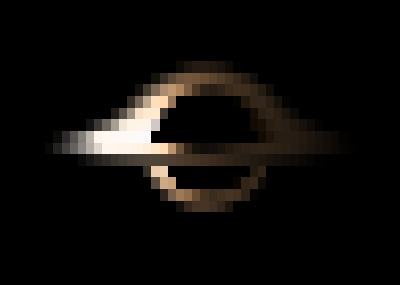

-Graphics-

```mathematica
image=Table[ColorPixel[nullGeodesics[[i,j]],rin,rout],{i,yres},{j,xres}];
ArrayPlot[image,AspectRatio->Δy/Δx,Frame->False,Background->Black]
GaussianFilter[%,20]
```

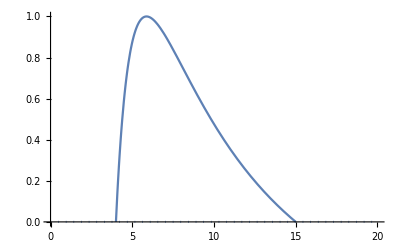

```mathematica
f[r_]:=(1/r^2-1/rout^2)(1-(rin/r)^(1/2))1/((1-3^(1/4) √(rin/(√(5 rout^2+(25 rin rout^4)/((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))+((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))/rin)-√(10 rout^2-(25 rin rout^4)/((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))-((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))/rin+(12 √3 rout^4)/(rin √(5 rout^2+(25 rin rout^4)/((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))+((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))/rin)))))) (-1/rout^2+3/(√(5 rout^2+(25 rin rout^4)/((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))+((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))/rin)-√(10 rout^2-(25 rin rout^4)/((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))-((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))/rin+(12 √3 rout^4)/(rin √(5 rout^2+(25 rin rout^4)/((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))+((125 rin^3 rout^6+54 rin rout^8+6 √(375 rin^4 rout^14+81 rin^2 rout^16))^(1/3))/rin))))^2));
ReImPlot[f[r],{r,0,20},PlotRange->{0,1}]
```